```mathematica
Clear["Global`*"]
```

```mathematica
Needs["Quantum`Notation`"]
```

```mathematica
SetQuantumAliases[];
```

## Asymmetric Quantum Walk

```mathematica
|w[0]⟩=|Subscript[0, ĉ]⟩⊗|Subscript[0, p̂]⟩
```

|0_(ĉ),0_(p̂)⟩

```mathematica
Ry[θ_]=Cos[θ/2]|Subscript[0, ĉ]⟩·⟨Subscript[0, ĉ]|+Sin[θ/2]|Subscript[1, ĉ]⟩·⟨Subscript[0, ĉ]|-Sin[θ/2]|Subscript[0, ĉ]⟩·⟨Subscript[1, ĉ]|+Cos[θ/2]|Subscript[1, ĉ]⟩·⟨Subscript[1, ĉ]|
```

Cos[θ/2] |0_(ĉ)⟩·⟨0_(ĉ)|+Sin[θ/2] |1_(ĉ)⟩·⟨0_(ĉ)|-Sin[θ/2] |0_(ĉ)⟩·⟨1_(ĉ)|+Cos[θ/2] |1_(ĉ)⟩·⟨1_(ĉ)|

```mathematica
DefineOperatorOnKets[
Tup,
{|Subscript[0, ĉ],Subscript[j_, p̂]⟩:>|Subscript[0, ĉ],Subscript[(j+1), p̂]⟩,
|Subscript[1, ĉ],Subscript[j_, p̂]⟩:>|Subscript[1, ĉ],Subscript[j, p̂]⟩
}
]
```

|0_(ĉ),j__(p̂)⟩:>|0_(ĉ),(j+1)_(p̂)⟩
|1_(ĉ),j__(p̂)⟩:>|1_(ĉ),j_(p̂)⟩

```mathematica
DefineOperatorOnKets[
Tdown,
{|Subscript[0, ĉ],Subscript[j_, p̂]⟩:>|Subscript[0, ĉ],Subscript[j, p̂]⟩,
|Subscript[1, ĉ],Subscript[j_, p̂]⟩:>|Subscript[1, ĉ],Subscript[(j-1), p̂]⟩
}
]
```

|0_(ĉ),j__(p̂)⟩:>|0_(ĉ),j_(p̂)⟩
|1_(ĉ),j__(p̂)⟩:>|1_(ĉ),(j-1)_(p̂)⟩

```mathematica
steps=60;
θ1 = -Pi/2;
θ2 = 3Pi/4;
increment = (11Pi/8-3Pi/4)/steps;
```

```mathematica
For[k=1,k≤ steps,k++,
	θ2 = θ2 + increment;
	|w[k]⟩=Expand[Tdown·Ry[θ2]·Tup·Ry[θ1]·|w[k-1]⟩]//N;
	]
```

```mathematica
|w[60]⟩
```

4.95608×10^-20 |0_(ĉ),-59_(p̂)⟩+6.47137×10^-18 |0_(ĉ),-58_(p̂)⟩+4.02257×10^-16 |0_(ĉ),-57_(p̂)⟩+1.58373×10^-14 |0_(ĉ),-56_(p̂)⟩+4.43255×10^-13 |0_(ĉ),-55_(p̂)⟩+9.38161×10^-12 |0_(ĉ),-54_(p̂)⟩+1.55935×10^-10 |0_(ĉ),-53_(p̂)⟩+2.08613×10^-9 |0_(ĉ),-52_(p̂)⟩+2.2835×10^-8 |0_(ĉ),-51_(p̂)⟩+2.06721×10^-7 |0_(ĉ),-50_(p̂)⟩+1.55751×10^-6 |0_(ĉ),-49_(p̂)⟩+9.78937×10^-6 |0_(ĉ),-48_(p̂)⟩+0.0000512384 |0_(ĉ),-47_(p̂)⟩+0.000221807 |0_(ĉ),-46_(p̂)⟩+0.000782667 |0_(ĉ),-45_(p̂)⟩+0.00218714 |0_(ĉ),-44_(p̂)⟩+0.00454172 |0_(ĉ),-43_(p̂)⟩+0.00575783 |0_(ĉ),-42_(p̂)⟩-0.000681757 |0_(ĉ),-41_(p̂)⟩-0.0224885 |0_(ĉ),-40_(p̂)⟩-0.0530144 |0_(ĉ),-39_(p̂)⟩-0.0564073 |0_(ĉ),-38_(p̂)⟩+0.00413745 |0_(ĉ),-37_(p̂)⟩+0.0922755 |0_(ĉ),-36_(p̂)⟩+0.101216 |0_(ĉ),-35_(p̂)⟩+0.0175684 |0_(ĉ),-34_(p̂)⟩-0.0102261 |0_(ĉ),-33_(p̂)⟩+0.0594893 |0_(ĉ),-32_(p̂)⟩+0.0452168 |0_(ĉ),-31_(p̂)⟩-0.0481869 |0_(ĉ),-30_(p̂)⟩-0.00924041 |0_(ĉ),-29_(p̂)⟩+0.034183 |0_(ĉ),-28_(p̂)⟩-0.0611821 |0_(ĉ),-27_(p̂)⟩-0.0345064 |0_(ĉ),-26_(p̂)⟩+0.0225888 |0_(ĉ),-25_(p̂)⟩-0.0744373 |0_(ĉ),-24_(p̂)⟩-0.0192156 |0_(ĉ),-23_(p̂)⟩+0.00832322 |0_(ĉ),-22_(p̂)⟩-0.0793599 |0_(ĉ),-21_(p̂)⟩+0.0230711 |0_(ĉ),-20_(p̂)⟩-0.0312123 |0_(ĉ),-19_(p̂)⟩-0.0389171 |0_(ĉ),-18_(p̂)⟩+0.0384731 |0_(ĉ),-17_(p̂)⟩-0.0658451 |0_(ĉ),-16_(p̂)⟩+0.0452193 |0_(ĉ),-15_(p̂)⟩-0.0276548 |0_(ĉ),-14_(p̂)⟩+0.00522379 |0_(ĉ),-13_(p̂)⟩+0.03142 |0_(ĉ),-12_(p̂)⟩-0.0328545 |0_(ĉ),-11_(p̂)⟩+0.0714988 |0_(ĉ),-10_(p̂)⟩-0.0457021 |0_(ĉ),-9_(p̂)⟩+0.0842083 |0_(ĉ),-8_(p̂)⟩-0.0370407 |0_(ĉ),-7_(p̂)⟩+0.079512 |0_(ĉ),-6_(p̂)⟩-0.019654 |0_(ĉ),-5_(p̂)⟩+0.0695066 |0_(ĉ),-4_(p̂)⟩-0.00389289 |0_(ĉ),-3_(p̂)⟩+0.062031 |0_(ĉ),-2_(p̂)⟩+0.00468059 |0_(ĉ),-1_(p̂)⟩+0.060952 |0_(ĉ),0_(p̂)⟩+0.00375238 |0_(ĉ),1_(p̂)⟩+0.0679774 |0_(ĉ),2_(p̂)⟩-0.00712634 |0_(ĉ),3_(p̂)⟩+0.0831761 |0_(ĉ),4_(p̂)⟩-0.025981 |0_(ĉ),5_(p̂)⟩+0.103184 |0_(ĉ),6_(p̂)⟩-0.0455747 |0_(ĉ),7_(p̂)⟩+0.117614 |0_(ĉ),8_(p̂)⟩-0.0501562 |0_(ĉ),9_(p̂)⟩+0.107605 |0_(ĉ),10_(p̂)⟩-0.0184815 |0_(ĉ),11_(p̂)⟩+0.0559937 |0_(ĉ),12_(p̂)⟩+0.056124 |0_(ĉ),13_(p̂)⟩-0.022985 |0_(ĉ),14_(p̂)⟩+0.131092 |0_(ĉ),15_(p̂)⟩-0.0572106 |0_(ĉ),16_(p̂)⟩+0.116553 |0_(ĉ),17_(p̂)⟩+0.029086 |0_(ĉ),18_(p̂)⟩-0.00678072 |0_(ĉ),19_(p̂)⟩+0.153769 |0_(ĉ),20_(p̂)⟩-0.054569 |0_(ĉ),21_(p̂)⟩+0.0861238 |0_(ĉ),22_(p̂)⟩+0.108452 |0_(ĉ),23_(p̂)⟩-0.0815369 |0_(ĉ),24_(p̂)⟩+0.123221 |0_(ĉ),25_(p̂)⟩+0.0629305 |0_(ĉ),26_(p̂)⟩-0.122205 |0_(ĉ),27_(p̂)⟩+0.0852976 |0_(ĉ),28_(p̂)⟩+0.0516045 |0_(ĉ),29_(p̂)⟩-0.202316 |0_(ĉ),30_(p̂)⟩-0.0713348 |0_(ĉ),31_(p̂)⟩+0.0751861 |0_(ĉ),32_(p̂)⟩-0.158642 |0_(ĉ),33_(p̂)⟩-0.309253 |0_(ĉ),34_(p̂)⟩-0.0663032 |0_(ĉ),35_(p̂)⟩+0.219707 |0_(ĉ),36_(p̂)⟩+0.233298 |0_(ĉ),37_(p̂)⟩+0.07583 |0_(ĉ),38_(p̂)⟩-0.0399759 |0_(ĉ),39_(p̂)⟩-0.0569398 |0_(ĉ),40_(p̂)⟩-0.029465 |0_(ĉ),41_(p̂)⟩-0.00626488 |0_(ĉ),42_(p̂)⟩+0.00215174 |0_(ĉ),43_(p̂)⟩+0.00261499 |0_(ĉ),44_(p̂)⟩+0.00134777 |0_(ĉ),45_(p̂)⟩+0.000484972 |0_(ĉ),46_(p̂)⟩+0.000135308 |0_(ĉ),47_(p̂)⟩+0.0000304949 |0_(ĉ),48_(p̂)⟩+5.6602×10^-6 |0_(ĉ),49_(p̂)⟩+8.73156×10^-7 |0_(ĉ),50_(p̂)⟩+1.12273×10^-7 |0_(ĉ),51_(p̂)⟩+1.20127×10^-8 |0_(ĉ),52_(p̂)⟩+1.06319×10^-9 |0_(ĉ),53_(p̂)⟩+7.7022×10^-11 |0_(ĉ),54_(p̂)⟩+4.4933×10^-12 |0_(ĉ),55_(p̂)⟩+2.05972×10^-13 |0_(ĉ),56_(p̂)⟩+7.14434×10^-15 |0_(ĉ),57_(p̂)⟩+1.76268×10^-16 |0_(ĉ),58_(p̂)⟩+2.75623×10^-18 |0_(ĉ),59_(p̂)⟩+2.05288×10^-20 |0_(ĉ),60_(p̂)⟩-2.05288×10^-20 |1_(ĉ),-60_(p̂)⟩-2.73859×10^-18 |1_(ĉ),-59_(p̂)⟩-1.73956×10^-16 |1_(ĉ),-58_(p̂)⟩-7.00032×10^-15 |1_(ĉ),-57_(p̂)⟩-2.00301×10^-13 |1_(ĉ),-56_(p̂)⟩-4.33498×10^-12 |1_(ĉ),-55_(p̂)⟩-7.36897×10^-11 |1_(ĉ),-54_(p̂)⟩-1.00832×10^-9 |1_(ĉ),-53_(p̂)⟩-1.12891×10^-8 |1_(ĉ),-52_(p̂)⟩-1.04515×10^-7 |1_(ĉ),-51_(p̂)⟩-8.04966×10^-7 |1_(ĉ),-50_(p̂)⟩-5.16742×10^-6 |1_(ĉ),-49_(p̂)⟩-0.0000275773 |1_(ĉ),-48_(p̂)⟩-0.000121328 |1_(ĉ),-47_(p̂)⟩-0.00043229 |1_(ĉ),-46_(p̂)⟩-0.00120221 |1_(ĉ),-45_(p̂)⟩-0.00238503 |1_(ĉ),-44_(p̂)⟩-0.0023416 |1_(ĉ),-43_(p̂)⟩+0.00376101 |1_(ĉ),-42_(p̂)⟩+0.0213628 |1_(ĉ),-41_(p̂)⟩+0.0436399 |1_(ĉ),-40_(p̂)⟩+0.037691 |1_(ĉ),-39_(p̂)⟩-0.0320017 |1_(ĉ),-38_(p̂)⟩-0.129545 |1_(ĉ),-37_(p̂)⟩-0.132828 |1_(ĉ),-36_(p̂)⟩-0.00105271 |1_(ĉ),-35_(p̂)⟩+0.0899552 |1_(ĉ),-34_(p̂)⟩+0.0121743 |1_(ĉ),-33_(p̂)⟩-0.0312665 |1_(ĉ),-32_(p̂)⟩+0.0879583 |1_(ĉ),-31_(p̂)⟩+0.0972951 |1_(ĉ),-30_(p̂)⟩-0.0198056 |1_(ĉ),-29_(p̂)⟩+0.0505013 |1_(ĉ),-28_(p̂)⟩+0.0988551 |1_(ĉ),-27_(p̂)⟩-0.0295634 |1_(ĉ),-26_(p̂)⟩+0.0366047 |1_(ĉ),-25_(p̂)⟩+0.069508 |1_(ĉ),-24_(p̂)⟩-0.0535734 |1_(ĉ),-23_(p̂)⟩+0.0521476 |1_(ĉ),-22_(p̂)⟩+0.0129119 |1_(ĉ),-21_(p̂)⟩-0.0495322 |1_(ĉ),-20_(p̂)⟩+0.0664455 |1_(ĉ),-19_(p̂)⟩-0.0600849 |1_(ĉ),-18_(p̂)⟩+0.0178607 |1_(ĉ),-17_(p̂)⟩+0.00675237 |1_(ĉ),-16_(p̂)⟩-0.053781 |1_(ĉ),-15_(p̂)⟩+0.0558497 |1_(ĉ),-14_(p̂)⟩-0.076576 |1_(ĉ),-13_(p̂)⟩+0.0519333 |1_(ĉ),-12_(p̂)⟩-0.0507108 |1_(ĉ),-11_(p̂)⟩+0.0167729 |1_(ĉ),-10_(p̂)⟩-0.00763264 |1_(ĉ),-9_(p̂)⟩-0.020111 |1_(ĉ),-8_(p̂)⟩+0.0294655 |1_(ĉ),-7_(p̂)⟩-0.044609 |1_(ĉ),-6_(p̂)⟩+0.0537919 |1_(ĉ),-5_(p̂)⟩-0.0560309 |1_(ĉ),-4_(p̂)⟩+0.0678224 |1_(ĉ),-3_(p̂)⟩-0.0587463 |1_(ĉ),-2_(p̂)⟩+0.0758033 |1_(ĉ),-1_(p̂)⟩-0.0565378 |1_(ĉ),0_(p̂)⟩+0.0798903 |1_(ĉ),1_(p̂)⟩-0.0502675 |1_(ĉ),2_(p̂)⟩+0.0788332 |1_(ĉ),3_(p̂)⟩-0.0373342 |1_(ĉ),4_(p̂)⟩+0.0680666 |1_(ĉ),5_(p̂)⟩-0.0125974 |1_(ĉ),6_(p̂)⟩+0.0418611 |1_(ĉ),7_(p̂)⟩+0.0276526 |1_(ĉ),8_(p̂)⟩-0.000335115 |1_(ĉ),9_(p̂)⟩+0.076818 |1_(ĉ),10_(p̂)⟩-0.0432796 |1_(ĉ),11_(p̂)⟩+0.108039 |1_(ĉ),12_(p̂)⟩-0.0512465 |1_(ĉ),13_(p̂)⟩+0.081321 |1_(ĉ),14_(p̂)⟩+0.00607739 |1_(ĉ),15_(p̂)⟩-0.00846608 |1_(ĉ),16_(p̂)⟩+0.0896531 |1_(ĉ),17_(p̂)⟩-0.0734647 |1_(ĉ),18_(p̂)⟩+0.0770939 |1_(ĉ),19_(p̂)⟩-0.00576269 |1_(ĉ),20_(p̂)⟩-0.0586305 |1_(ĉ),21_(p̂)⟩+0.0847448 |1_(ĉ),22_(p̂)⟩-0.084802 |1_(ĉ),23_(p̂)⟩-0.0389976 |1_(ĉ),24_(p̂)⟩+0.0546049 |1_(ĉ),25_(p̂)⟩-0.129868 |1_(ĉ),26_(p̂)⟩-0.0601233 |1_(ĉ),27_(p̂)⟩+0.0427409 |1_(ĉ),28_(p̂)⟩-0.133721 |1_(ĉ),29_(p̂)⟩-0.122067 |1_(ĉ),30_(p̂)⟩+0.0578497 |1_(ĉ),31_(p̂)⟩-0.0134031 |1_(ĉ),32_(p̂)⟩-0.140828 |1_(ĉ),33_(p̂)⟩-0.0010509 |1_(ĉ),34_(p̂)⟩+0.208051 |1_(ĉ),35_(p̂)⟩+0.202409 |1_(ĉ),36_(p̂)⟩+0.0441324 |1_(ĉ),37_(p̂)⟩-0.0679802 |1_(ĉ),38_(p̂)⟩-0.074425 |1_(ĉ),39_(p̂)⟩-0.0347129 |1_(ĉ),40_(p̂)⟩-0.0043406 |1_(ĉ),41_(p̂)⟩+0.00558148 |1_(ĉ),42_(p̂)⟩+0.00496632 |1_(ĉ),43_(p̂)⟩+0.00244671 |1_(ĉ),44_(p̂)⟩+0.00087748 |1_(ĉ),45_(p̂)⟩+0.000247439 |1_(ĉ),46_(p̂)⟩+0.0000567063 |1_(ĉ),47_(p̂)⟩+0.0000107346 |1_(ĉ),48_(p̂)⟩+1.69144×10^-6 |1_(ĉ),49_(p̂)⟩+2.22326×10^-7 |1_(ĉ),50_(p̂)⟩+2.43255×10^-8 |1_(ĉ),51_(p̂)⟩+2.20184×10^-9 |1_(ĉ),52_(p̂)⟩+1.63128×10^-10 |1_(ĉ),53_(p̂)⟩+9.73128×10^-12 |1_(ĉ),54_(p̂)⟩+4.56066×10^-13 |1_(ĉ),55_(p̂)⟩+1.61701×10^-14 |1_(ĉ),56_(p̂)⟩+4.07719×10^-16 |1_(ĉ),57_(p̂)⟩+6.51396×10^-18 |1_(ĉ),58_(p̂)⟩+4.95608×10^-20 |1_(ĉ),59_(p̂)⟩

```mathematica
Do[
With[{j=pos},
DefineOperatorOnKets[
pp[j],
{(|Subscript[n_, ĉ],Subscript[k_, p̂]⟩/;k=!=j):>0,
|Subscript[n_, ĉ],Subscript[j, p̂]⟩:>|Subscript[n, ĉ],Subscript[j, p̂]⟩
} ]],
{pos,-steps,steps}]
```

```mathematica
probabilities=
Table[{j,⟨w[steps]|·pp[j]·|w[steps]⟩},{j,-steps,steps}]
```

{{-60,0.},{-59,8.70379×10^-102},{-58,2.45157×10^-98},{-57,4.21269×10^-93},{-56,1.28703×10^-89},{-55,1.26917×10^-85},{-54,4.92973×10^-82},{-53,4.87244×10^-79},{-52,3.34389×10^-75},{-51,1.37251×10^-73},{-50,5.69588×10^-69},{-49,2.4997×10^-67},{-48,2.78067×10^-63},{-47,6.61142×10^-61},{-46,3.6308×10^-58},{-45,2.46801×10^-55},{-44,5.9604×10^-54},{-43,2.46202×10^-50},{-42,4.59584×10^-49},{-41,6.46766×10^-46},{-40,8.02722×10^-44},{-39,2.14515×10^-42},{-38,1.59853×10^-39},{-37,2.07991×10^-38},{-36,4.04851×10^-36},{-35,4.3792×10^-34},{-34,2.25996×10^-33},{-33,2.54516×10^-31},{-32,2.36275×10^-29},{-31,5.3618×10^-28},{-30,3.44126×10^-27},{-29,2.06674×10^-26},{-28,5.67536×10^-24},{-27,2.84939×10^-22},{-26,8.36055×10^-21},{-25,1.81271×10^-19},{-24,3.28328×10^-18},{-23,5.39046×10^-17},{-22,8.52699×10^-16},{-21,1.37851×10^-14},{-20,2.32606×10^-13},{-19,4.04694×10^-12},{-18,6.89139×10^-11},{-17,1.06616×10^-9},{-16,1.37276×10^-8},{-15,1.30854×10^-7},{-14,7.53907×10^-7},{-13,1.43434×10^-6},{-12,7.36161×10^-6},{-11,0.000344182},{-10,0.00312609},{-9,0.0078087},{-8,0.00436047},{-7,0.080447},{-6,0.18103},{-5,0.0426529},{-4,0.0686527},{-3,0.0309982},{-2,0.0670297},{-1,0.0445342},{0,0.0836913},{1,0.045177},{2,0.105586},{3,0.00667356},{4,0.0379566},{5,0.112213},{6,0.0186048},{7,0.0351714},{8,0.0212083},{9,0.00252909},{10,0.0000614425},{11,0.0000969729},{12,0.0000321658},{13,4.51401×10^-6},{14,3.59721×10^-7},{15,1.70858×10^-8},{16,4.18905×10^-10},{17,1.80878×10^-12},{18,5.30425×10^-13},{19,1.25205×10^-13},{20,1.18154×10^-14},{21,6.36111×10^-16},{22,1.80766×10^-17},{23,8.30881×10^-20},{24,6.23906×10^-20},{25,1.71054×10^-20},{26,2.1497×10^-21},{27,1.65455×10^-22},{28,8.52555×10^-24},{29,2.52004×10^-25},{30,2.24935×10^-27},{31,3.2741×10^-29},{32,1.18721×10^-29},{33,5.65397×10^-31},{34,2.55499×10^-33},{35,1.77348×10^-34},{36,7.39203×10^-36},{37,3.93509×10^-39},{38,1.19231×10^-39},{39,7.83432×10^-42},{40,2.83728×10^-44},{41,8.35646×10^-46},{42,5.39553×10^-50},{43,2.16165×10^-50},{44,2.34822×10^-53},{45,1.64902×10^-55},{46,5.36756×10^-58},{47,3.07875×10^-61},{48,3.06325×10^-63},{49,2.35165×10^-68},{50,5.4473×10^-69},{51,4.3265×10^-73},{52,2.95613×10^-75},{53,6.57042×10^-79},{54,4.16703×10^-82},{55,1.40259×10^-85},{56,1.06259×10^-89},{57,4.31691×10^-93},{58,2.00648×10^-98},{59,8.70379×10^-102},{60,0.}}

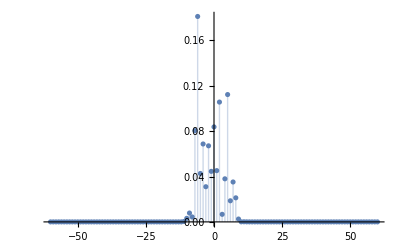

```mathematica
ListPlot[probabilities,PlotRange->All,Filling->Axis]
```

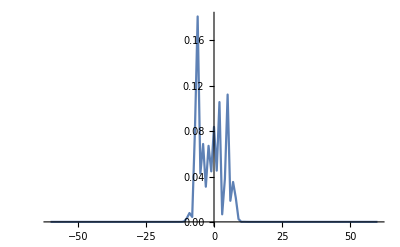

```mathematica
ListPlot[probabilities,PlotRange->All,Joined->True]
```

```mathematica
Abs[Tan[θ2/2]/Tan[θ1/2]]//N
```

2.41421

```mathematica
Abs[Tan[(Pi/4)/2]/Tan[θ1/2]]//N
```

0.414214

```mathematica
qm= QuantumMeasurement[|w[steps]⟩,{p̂},FactorKet->False]
```

0

```mathematica
N[qm]
```

Probability | Measurement | State
0. | {{-42_(p̂)}} | -0.68362 |0_(ĉ),-42_(p̂)⟩+0.729838 |1_(ĉ),-42_(p̂)⟩
0. | {{-41_(p̂)}} | -0.594332 |0_(ĉ),-41_(p̂)⟩-0.804219 |1_(ĉ),-41_(p̂)⟩
0. | {{-40_(p̂)}} | 0.04546 |0_(ĉ),-40_(p̂)⟩-0.998966 |1_(ĉ),-40_(p̂)⟩
0. | {{-39_(p̂)}} | 0.404056 |0_(ĉ),-39_(p̂)⟩-0.914734 |1_(ĉ),-39_(p̂)⟩
0. | {{-38_(p̂)}} | 0.851293 |0_(ĉ),-38_(p̂)⟩-0.524691 |1_(ĉ),-38_(p̂)⟩
0. | {{-37_(p̂)}} | 0.708437 |0_(ĉ),-37_(p̂)⟩+0.705774 |1_(ĉ),-37_(p̂)⟩
0. | {{-36_(p̂)}} | -0.00390395 |0_(ĉ),-36_(p̂)⟩+0.999992 |1_(ĉ),-36_(p̂)⟩
0. | {{-35_(p̂)}} | -0.416503 |0_(ĉ),-35_(p̂)⟩+0.909134 |1_(ĉ),-35_(p̂)⟩
0. | {{-34_(p̂)}} | -0.75335 |0_(ĉ),-34_(p̂)⟩+0.65762 |1_(ĉ),-34_(p̂)⟩
0. | {{-33_(p̂)}} | -0.994006 |0_(ĉ),-33_(p̂)⟩+0.109323 |1_(ĉ),-33_(p̂)⟩
0. | {{-32_(p̂)}} | -0.698035 |0_(ĉ),-32_(p̂)⟩-0.716063 |1_(ĉ),-32_(p̂)⟩
0. | {{-31_(p̂)}} | 0.0102829 |0_(ĉ),-31_(p̂)⟩-0.999947 |1_(ĉ),-31_(p̂)⟩
0. | {{-30_(p̂)}} | 0.470097 |0_(ĉ),-30_(p̂)⟩-0.882615 |1_(ĉ),-30_(p̂)⟩
0. | {{-29_(p̂)}} | 0.725554 |0_(ĉ),-29_(p̂)⟩-0.688166 |1_(ĉ),-29_(p̂)⟩
0. | {{-28_(p̂)}} | 0.868643 |0_(ĉ),-28_(p̂)⟩-0.495439 |1_(ĉ),-28_(p̂)⟩
0. | {{-27_(p̂)}} | 0.946123 |0_(ĉ),-27_(p̂)⟩-0.323807 |1_(ĉ),-27_(p̂)⟩
0. | {{-26_(p̂)}} | 0.984136 |0_(ĉ),-26_(p̂)⟩-0.177417 |1_(ĉ),-26_(p̂)⟩
0. | {{-25_(p̂)}} | 0.998491 |0_(ĉ),-25_(p̂)⟩-0.0549184 |1_(ĉ),-25_(p̂)⟩
0. | {{-24_(p̂)}} | 0.998897 |0_(ĉ),-24_(p̂)⟩+0.0469559 |1_(ĉ),-24_(p̂)⟩
0. | {{-23_(p̂)}} | 0.991278 |0_(ĉ),-23_(p̂)⟩+0.131789 |1_(ĉ),-23_(p̂)⟩
0. | {{-22_(p̂)}} | 0.979215 |0_(ĉ),-22_(p̂)⟩+0.202826 |1_(ĉ),-22_(p̂)⟩
0. | {{-21_(p̂)}} | 0.964856 |0_(ĉ),-21_(p̂)⟩+0.262778 |1_(ĉ),-21_(p̂)⟩
1.24112×10^-10 | {{-20_(p̂)}} | 0.94948 |0_(ĉ),-20_(p̂)⟩+0.313828 |1_(ĉ),-20_(p̂)⟩
1.06172×10^-9 | {{-19_(p̂)}} | 0.933834 |0_(ĉ),-19_(p̂)⟩+0.357706 |1_(ĉ),-19_(p̂)⟩
7.9126×10^-9 | {{-18_(p̂)}} | 0.918349 |0_(ĉ),-18_(p̂)⟩+0.395772 |1_(ĉ),-18_(p̂)⟩
5.16491×10^-8 | {{-17_(p̂)}} | 0.903257 |0_(ĉ),-17_(p̂)⟩+0.4291 |1_(ĉ),-17_(p̂)⟩
2.96689×10^-7 | {{-16_(p̂)}} | 0.888675 |0_(ĉ),-16_(p̂)⟩+0.458537 |1_(ĉ),-16_(p̂)⟩
1.50616×10^-6 | {{-15_(p̂)}} | 0.874648 |0_(ĉ),-15_(p̂)⟩+0.484759 |1_(ĉ),-15_(p̂)⟩
6.78282×10^-6 | {{-14_(p̂)}} | 0.861176 |0_(ĉ),-14_(p̂)⟩+0.508306 |1_(ĉ),-14_(p̂)⟩
0.0000271879 | {{-13_(p̂)}} | 0.848237 |0_(ĉ),-13_(p̂)⟩+0.529617 |1_(ĉ),-13_(p̂)⟩
0.000097289 | {{-12_(p̂)}} | 0.835792 |0_(ĉ),-12_(p̂)⟩+0.549046 |1_(ĉ),-12_(p̂)⟩
0.000311623 | {{-11_(p̂)}} | 0.823795 |0_(ĉ),-11_(p̂)⟩+0.566888 |1_(ĉ),-11_(p̂)⟩
0.000895564 | {{-10_(p̂)}} | 0.812197 |0_(ĉ),-10_(p̂)⟩+0.583383 |1_(ĉ),-10_(p̂)⟩
0.00231403 | {{-9_(p̂)}} | 0.800947 |0_(ĉ),-9_(p̂)⟩+0.598735 |1_(ĉ),-9_(p̂)⟩
0.00538564 | {{-8_(p̂)}} | 0.789993 |0_(ĉ),-8_(p̂)⟩+0.613115 |1_(ĉ),-8_(p̂)⟩
0.0113083 | {{-7_(p̂)}} | 0.779286 |0_(ĉ),-7_(p̂)⟩+0.626668 |1_(ĉ),-7_(p̂)⟩
0.0214506 | {{-6_(p̂)}} | 0.768776 |0_(ĉ),-6_(p̂)⟩+0.639519 |1_(ĉ),-6_(p̂)⟩
0.0368024 | {{-5_(p̂)}} | 0.758413 |0_(ĉ),-5_(p̂)⟩+0.651774 |1_(ĉ),-5_(p̂)⟩
0.0571643 | {{-4_(p̂)}} | 0.748149 |0_(ĉ),-4_(p̂)⟩+0.663531 |1_(ĉ),-4_(p̂)⟩
0.0804502 | {{-3_(p̂)}} | 0.737936 |0_(ĉ),-3_(p̂)⟩+0.67487 |1_(ĉ),-3_(p̂)⟩
0.102647 | {{-2_(p̂)}} | 0.727725 |0_(ĉ),-2_(p̂)⟩+0.685869 |1_(ĉ),-2_(p̂)⟩
0.118785 | {{-1_(p̂)}} | 0.717466 |0_(ĉ),-1_(p̂)⟩+0.696594 |1_(ĉ),-1_(p̂)⟩
0.124706 | {{0_(p̂)}} | 0.707107 |0_(ĉ),0_(p̂)⟩+0.707107 |1_(ĉ),0_(p̂)⟩
0.118785 | {{1_(p̂)}} | 0.696594 |0_(ĉ),1_(p̂)⟩+0.717466 |1_(ĉ),1_(p̂)⟩
0.102647 | {{2_(p̂)}} | 0.685869 |0_(ĉ),2_(p̂)⟩+0.727725 |1_(ĉ),2_(p̂)⟩
0.0804502 | {{3_(p̂)}} | 0.67487 |0_(ĉ),3_(p̂)⟩+0.737936 |1_(ĉ),3_(p̂)⟩
0.0571643 | {{4_(p̂)}} | 0.663531 |0_(ĉ),4_(p̂)⟩+0.748149 |1_(ĉ),4_(p̂)⟩
0.0368024 | {{5_(p̂)}} | 0.651774 |0_(ĉ),5_(p̂)⟩+0.758413 |1_(ĉ),5_(p̂)⟩
0.0214506 | {{6_(p̂)}} | 0.639519 |0_(ĉ),6_(p̂)⟩+0.768776 |1_(ĉ),6_(p̂)⟩
0.0113083 | {{7_(p̂)}} | 0.626668 |0_(ĉ),7_(p̂)⟩+0.779286 |1_(ĉ),7_(p̂)⟩
0.00538564 | {{8_(p̂)}} | 0.613115 |0_(ĉ),8_(p̂)⟩+0.789993 |1_(ĉ),8_(p̂)⟩
0.00231403 | {{9_(p̂)}} | 0.598735 |0_(ĉ),9_(p̂)⟩+0.800947 |1_(ĉ),9_(p̂)⟩
0.000895564 | {{10_(p̂)}} | 0.583383 |0_(ĉ),10_(p̂)⟩+0.812197 |1_(ĉ),10_(p̂)⟩
0.000311623 | {{11_(p̂)}} | 0.566888 |0_(ĉ),11_(p̂)⟩+0.823795 |1_(ĉ),11_(p̂)⟩
0.000097289 | {{12_(p̂)}} | 0.549046 |0_(ĉ),12_(p̂)⟩+0.835792 |1_(ĉ),12_(p̂)⟩
0.0000271879 | {{13_(p̂)}} | 0.529617 |0_(ĉ),13_(p̂)⟩+0.848237 |1_(ĉ),13_(p̂)⟩
6.78282×10^-6 | {{14_(p̂)}} | 0.508306 |0_(ĉ),14_(p̂)⟩+0.861176 |1_(ĉ),14_(p̂)⟩
1.50616×10^-6 | {{15_(p̂)}} | 0.484759 |0_(ĉ),15_(p̂)⟩+0.874648 |1_(ĉ),15_(p̂)⟩
2.96689×10^-7 | {{16_(p̂)}} | 0.458537 |0_(ĉ),16_(p̂)⟩+0.888675 |1_(ĉ),16_(p̂)⟩
5.16491×10^-8 | {{17_(p̂)}} | 0.4291 |0_(ĉ),17_(p̂)⟩+0.903257 |1_(ĉ),17_(p̂)⟩
7.9126×10^-9 | {{18_(p̂)}} | 0.395772 |0_(ĉ),18_(p̂)⟩+0.918349 |1_(ĉ),18_(p̂)⟩
1.06172×10^-9 | {{19_(p̂)}} | 0.357706 |0_(ĉ),19_(p̂)⟩+0.933834 |1_(ĉ),19_(p̂)⟩
1.24112×10^-10 | {{20_(p̂)}} | 0.313828 |0_(ĉ),20_(p̂)⟩+0.94948 |1_(ĉ),20_(p̂)⟩
0. | {{21_(p̂)}} | 0.262778 |0_(ĉ),21_(p̂)⟩+0.964856 |1_(ĉ),21_(p̂)⟩
0. | {{22_(p̂)}} | 0.202826 |0_(ĉ),22_(p̂)⟩+0.979215 |1_(ĉ),22_(p̂)⟩
0. | {{23_(p̂)}} | 0.131789 |0_(ĉ),23_(p̂)⟩+0.991278 |1_(ĉ),23_(p̂)⟩
0. | {{24_(p̂)}} | 0.0469559 |0_(ĉ),24_(p̂)⟩+0.998897 |1_(ĉ),24_(p̂)⟩
0. | {{25_(p̂)}} | -0.0549184 |0_(ĉ),25_(p̂)⟩+0.998491 |1_(ĉ),25_(p̂)⟩
0. | {{26_(p̂)}} | -0.177417 |0_(ĉ),26_(p̂)⟩+0.984136 |1_(ĉ),26_(p̂)⟩
0. | {{27_(p̂)}} | -0.323807 |0_(ĉ),27_(p̂)⟩+0.946123 |1_(ĉ),27_(p̂)⟩
0. | {{28_(p̂)}} | -0.495439 |0_(ĉ),28_(p̂)⟩+0.868643 |1_(ĉ),28_(p̂)⟩
0. | {{29_(p̂)}} | -0.688166 |0_(ĉ),29_(p̂)⟩+0.725554 |1_(ĉ),29_(p̂)⟩
0. | {{30_(p̂)}} | -0.882615 |0_(ĉ),30_(p̂)⟩+0.470097 |1_(ĉ),30_(p̂)⟩
0. | {{31_(p̂)}} | -0.999947 |0_(ĉ),31_(p̂)⟩+0.0102829 |1_(ĉ),31_(p̂)⟩
0. | {{32_(p̂)}} | -0.716063 |0_(ĉ),32_(p̂)⟩-0.698035 |1_(ĉ),32_(p̂)⟩
0. | {{33_(p̂)}} | 0.109323 |0_(ĉ),33_(p̂)⟩-0.994006 |1_(ĉ),33_(p̂)⟩
0. | {{34_(p̂)}} | 0.65762 |0_(ĉ),34_(p̂)⟩-0.75335 |1_(ĉ),34_(p̂)⟩
0. | {{35_(p̂)}} | 0.909134 |0_(ĉ),35_(p̂)⟩-0.416503 |1_(ĉ),35_(p̂)⟩
0. | {{36_(p̂)}} | 0.999992 |0_(ĉ),36_(p̂)⟩-0.00390395 |1_(ĉ),36_(p̂)⟩
0. | {{37_(p̂)}} | 0.705774 |0_(ĉ),37_(p̂)⟩+0.708437 |1_(ĉ),37_(p̂)⟩
0. | {{38_(p̂)}} | -0.524691 |0_(ĉ),38_(p̂)⟩+0.851293 |1_(ĉ),38_(p̂)⟩
0. | {{39_(p̂)}} | -0.914734 |0_(ĉ),39_(p̂)⟩+0.404056 |1_(ĉ),39_(p̂)⟩
0. | {{40_(p̂)}} | -0.998966 |0_(ĉ),40_(p̂)⟩+0.04546 |1_(ĉ),40_(p̂)⟩
0. | {{41_(p̂)}} | -0.804219 |0_(ĉ),41_(p̂)⟩-0.594332 |1_(ĉ),41_(p̂)⟩
0. | {{42_(p̂)}} | 0.729838 |0_(ĉ),42_(p̂)⟩-0.68362 |1_(ĉ),42_(p̂)⟩
Probability | Measurement | State

```mathematica
probability={}
```

{}

```mathematica
For[i=1,i≤ Length[Flatten[qm[[1,All,2]]]],i++,
	AppendTo[probability,{Flatten[N[qm][[1,All,2]]][[i]],N[qm][[1,All,1]][[i]]}];
	]
```

```mathematica
qm[[1,All,1]][[40]]
```

0.0804502

```mathematica
probability
```

{{-42_(p̂),0},{-41_(p̂),0},{-40_(p̂),0},{-39_(p̂),0},{-38_(p̂),0},{-37_(p̂),0},{-36_(p̂),0},{-35_(p̂),0},{-34_(p̂),0},{-33_(p̂),0},{-32_(p̂),0},{-31_(p̂),0},{-30_(p̂),0},{-29_(p̂),0},{-28_(p̂),0},{-27_(p̂),0},{-26_(p̂),0},{-25_(p̂),0},{-24_(p̂),0},{-23_(p̂),0},{-22_(p̂),0},{-21_(p̂),0},{-20_(p̂),1.24112×10^-10},{-19_(p̂),1.06172×10^-9},{-18_(p̂),7.9126×10^-9},{-17_(p̂),5.16491×10^-8},{-16_(p̂),2.96689×10^-7},{-15_(p̂),1.50616×10^-6},{-14_(p̂),6.78282×10^-6},{-13_(p̂),0.0000271879},{-12_(p̂),0.000097289},{-11_(p̂),0.000311623},{-10_(p̂),0.000895564},{-9_(p̂),0.00231403},{-8_(p̂),0.00538564},{-7_(p̂),0.0113083},{-6_(p̂),0.0214506},{-5_(p̂),0.0368024},{-4_(p̂),0.0571643},{-3_(p̂),0.0804502},{-2_(p̂),0.102647},{-1_(p̂),0.118785},{0_(p̂),0.124706},{1_(p̂),0.118785},{2_(p̂),0.102647},{3_(p̂),0.0804502},{4_(p̂),0.0571643},{5_(p̂),0.0368024},{6_(p̂),0.0214506},{7_(p̂),0.0113083},{8_(p̂),0.00538564},{9_(p̂),0.00231403},{10_(p̂),0.000895564},{11_(p̂),0.000311623},{12_(p̂),0.000097289},{13_(p̂),0.0000271879},{14_(p̂),6.78282×10^-6},{15_(p̂),1.50616×10^-6},{16_(p̂),2.96689×10^-7},{17_(p̂),5.16491×10^-8},{18_(p̂),7.9126×10^-9},{19_(p̂),1.06172×10^-9},{20_(p̂),1.24112×10^-10},{21_(p̂),0},{22_(p̂),0},{23_(p̂),0},{24_(p̂),0},{25_(p̂),0},{26_(p̂),0},{27_(p̂),0},{28_(p̂),0},{29_(p̂),0},{30_(p̂),0},{31_(p̂),0},{32_(p̂),0},{33_(p̂),0},{34_(p̂),0},{35_(p̂),0},{36_(p̂),0},{37_(p̂),0},{38_(p̂),0},{39_(p̂),0},{40_(p̂),0},{41_(p̂),0},{42_(p̂),0}}

```mathematica
N[qm][[1,All,1]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.24112×10^-10,1.06172×10^-9,7.9126×10^-9,5.16491×10^-8,2.96689×10^-7,1.50616×10^-6,6.78282×10^-6,0.0000271879,0.000097289,0.000311623,0.000895564,0.00231403,0.00538564,0.0113083,0.0214506,0.0368024,0.0571643,0.0804502,0.102647,0.118785,0.124706,0.118785,0.102647,0.0804502,0.0571643,0.0368024,0.0214506,0.0113083,0.00538564,0.00231403,0.000895564,0.000311623,0.000097289,0.0000271879,6.78282×10^-6,1.50616×10^-6,2.96689×10^-7,5.16491×10^-8,7.9126×10^-9,1.06172×10^-9,1.24112×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
probabilities
```

{{-60,0.},{-59,3.13965×10^-69},{-58,3.72431×10^-65},{-57,3.19444×10^-62},{-56,1.8734×10^-57},{-55,1.99933×10^-54},{-54,1.40137×10^-51},{-53,1.08753×10^-47},{-52,3.61721×10^-45},{-51,1.37694×10^-42},{-50,4.30218×10^-39},{-49,8.9744×10^-37},{-48,9.48551×10^-35},{-47,2.31962×10^-31},{-46,4.71623×10^-29},{-45,1.2611×10^-27},{-44,2.08576×10^-24},{-43,5.46574×10^-22},{-42,2.87771×10^-20},{-41,2.69678×10^-18},{-40,1.17679×10^-15},{-39,1.34012×10^-13},{-38,5.39138×10^-12},{-37,3.35337×10^-10},{-36,6.76251×10^-8},{-35,6.65513×10^-6},{-34,0.000344589},{-33,0.0115339},{-32,0.475522},{-31,38.1621},{-30,2942.6},{-29,170357.},{-28,7.52344×10^6},{-27,2.61528×10^8},{-26,7.3173×10^9},{-25,1.67484×10^11},{-24,3.17721×10^12},{-23,5.05128×10^13},{-22,6.79627×10^14},{-21,7.80536×10^15},{-20,7.7105×10^16},{-19,6.59595×10^17},{-18,4.91572×10^18},{-17,3.20871×10^19},{-16,1.84319×10^20},{-15,9.35707×10^20},{-14,4.21385×10^21},{-13,1.68905×10^22},{-12,6.0441×10^22},{-11,1.93597×10^23},{-10,5.56372×10^23},{-9,1.43759×10^24},{-8,3.34584×10^24},{-7,7.02529×10^24},{-6,1.33263×10^25},{-5,2.28636×10^25},{-4,3.55135×10^25},{-3,4.99799×10^25},{-2,6.37694×10^25},{-1,7.37953×10^25},{0,7.74739×10^25},{1,7.37953×10^25},{2,6.37694×10^25},{3,4.99799×10^25},{4,3.55135×10^25},{5,2.28636×10^25},{6,1.33263×10^25},{7,7.02529×10^24},{8,3.34584×10^24},{9,1.43759×10^24},{10,5.56372×10^23},{11,1.93597×10^23},{12,6.0441×10^22},{13,1.68905×10^22},{14,4.21385×10^21},{15,9.35707×10^20},{16,1.84319×10^20},{17,3.20871×10^19},{18,4.91572×10^18},{19,6.59595×10^17},{20,7.7105×10^16},{21,7.80536×10^15},{22,6.79627×10^14},{23,5.05128×10^13},{24,3.17721×10^12},{25,1.67484×10^11},{26,7.3173×10^9},{27,2.61528×10^8},{28,7.52344×10^6},{29,170357.},{30,2942.6},{31,38.1621},{32,0.475522},{33,0.0115339},{34,0.000344589},{35,6.65513×10^-6},{36,6.76251×10^-8},{37,3.35337×10^-10},{38,5.39138×10^-12},{39,1.34012×10^-13},{40,1.17679×10^-15},{41,2.69678×10^-18},{42,2.87771×10^-20},{43,5.46574×10^-22},{44,2.08576×10^-24},{45,1.2611×10^-27},{46,4.71623×10^-29},{47,2.31962×10^-31},{48,9.48551×10^-35},{49,8.9744×10^-37},{50,4.30218×10^-39},{51,1.37694×10^-42},{52,3.61721×10^-45},{53,1.08753×10^-47},{54,1.40137×10^-51},{55,1.99933×10^-54},{56,1.8734×10^-57},{57,3.19444×10^-62},{58,3.72431×10^-65},{59,3.13965×10^-69},{60,0.}}

```mathematica
probability
```

{{-42_(p̂),0.},{-41_(p̂),0.},{-40_(p̂),0.},{-39_(p̂),0.},{-38_(p̂),0.},{-37_(p̂),0.},{-36_(p̂),0.},{-35_(p̂),0.},{-34_(p̂),0.},{-33_(p̂),0.},{-32_(p̂),0.},{-31_(p̂),0.},{-30_(p̂),0.},{-29_(p̂),0.},{-28_(p̂),0.},{-27_(p̂),0.},{-26_(p̂),0.},{-25_(p̂),0.},{-24_(p̂),0.},{-23_(p̂),0.},{-22_(p̂),0.},{-21_(p̂),0.},{-20_(p̂),1.24112×10^-10},{-19_(p̂),1.06172×10^-9},{-18_(p̂),7.9126×10^-9},{-17_(p̂),5.16491×10^-8},{-16_(p̂),2.96689×10^-7},{-15_(p̂),1.50616×10^-6},{-14_(p̂),6.78282×10^-6},{-13_(p̂),0.0000271879},{-12_(p̂),0.000097289},{-11_(p̂),0.000311623},{-10_(p̂),0.000895564},{-9_(p̂),0.00231403},{-8_(p̂),0.00538564},{-7_(p̂),0.0113083},{-6_(p̂),0.0214506},{-5_(p̂),0.0368024},{-4_(p̂),0.0571643},{-3_(p̂),0.0804502},{-2_(p̂),0.102647},{-1_(p̂),0.118785},{0_(p̂),0.124706},{1_(p̂),0.118785},{2_(p̂),0.102647},{3_(p̂),0.0804502},{4_(p̂),0.0571643},{5_(p̂),0.0368024},{6_(p̂),0.0214506},{7_(p̂),0.0113083},{8_(p̂),0.00538564},{9_(p̂),0.00231403},{10_(p̂),0.000895564},{11_(p̂),0.000311623},{12_(p̂),0.000097289},{13_(p̂),0.0000271879},{14_(p̂),6.78282×10^-6},{15_(p̂),1.50616×10^-6},{16_(p̂),2.96689×10^-7},{17_(p̂),5.16491×10^-8},{18_(p̂),7.9126×10^-9},{19_(p̂),1.06172×10^-9},{20_(p̂),1.24112×10^-10},{21_(p̂),0.},{22_(p̂),0.},{23_(p̂),0.},{24_(p̂),0.},{25_(p̂),0.},{26_(p̂),0.},{27_(p̂),0.},{28_(p̂),0.},{29_(p̂),0.},{30_(p̂),0.},{31_(p̂),0.},{32_(p̂),0.},{33_(p̂),0.},{34_(p̂),0.},{35_(p̂),0.},{36_(p̂),0.},{37_(p̂),0.},{38_(p̂),0.},{39_(p̂),0.},{40_(p̂),0.},{41_(p̂),0.},{42_(p̂),0.}}

```mathematica
ListPlot[probability,PlotRange->All,Joined->True]
```

-Graphics-

## Symmetric Quantum Walk

```mathematica
|w[0]⟩=1/(√2)(|Subscript[0, ĉ]⟩+I |Subscript[1, ĉ]⟩)⊗|Subscript[0, p̂]⟩
```

(|0_(ĉ),0_(p̂)⟩+ⅈ |1_(ĉ),0_(p̂)⟩)/(√2)

```mathematica
DefineOperatorOnKets[
h,
{|Subscript[0, ĉ]⟩:>(|Subscript[0, ĉ]⟩+|Subscript[1, ĉ]⟩)/(√2),
|Subscript[1, ĉ]⟩:>(|Subscript[0, ĉ]⟩-|Subscript[1, ĉ]⟩)/(√2)}]
```

|0_(ĉ)⟩:>(|0_(ĉ)⟩+|1_(ĉ)⟩)/(√2)
|1_(ĉ)⟩:>(|0_(ĉ)⟩-|1_(ĉ)⟩)/(√2)

```mathematica
DefineOperatorOnKets[
s,
{|Subscript[0, ĉ],Subscript[j_, p̂]⟩:>|Subscript[0, ĉ],Subscript[(j-1), p̂]⟩,
|Subscript[1, ĉ],Subscript[j_, p̂]⟩:>|Subscript[1, ĉ],Subscript[(j+1), p̂]⟩
}
]
```

|0_(ĉ),j__(p̂)⟩:>|0_(ĉ),(j-1)_(p̂)⟩
|1_(ĉ),j__(p̂)⟩:>|1_(ĉ),(j+1)_(p̂)⟩

```mathematica
steps=100;
Do[|w[k]⟩=Expand[s·h·|w[k-1]⟩],
{k,1,steps,1}];
```

```mathematica
|w[2]⟩
```

((1/2+ⅈ/2) |0_(ĉ),-2_(p̂)⟩)/(√2)+((1/2-ⅈ/2) |0_(ĉ),0_(p̂)⟩)/(√2)+((1/2+ⅈ/2) |1_(ĉ),0_(p̂)⟩)/(√2)-((1/2-ⅈ/2) |1_(ĉ),2_(p̂)⟩)/(√2)

```mathematica
|w[5]⟩
```

(1/8+ⅈ/8) |0_(ĉ),-5_(p̂)⟩+(1/2+ⅈ/4) |0_(ĉ),-3_(p̂)⟩-1/4 ⅈ |0_(ĉ),-1_(p̂)⟩+1/4 ⅈ |0_(ĉ),1_(p̂)⟩-(1/8-ⅈ/8) |0_(ĉ),3_(p̂)⟩+(1/8+ⅈ/8) |1_(ĉ),-3_(p̂)⟩+1/4 |1_(ĉ),-1_(p̂)⟩-1/4 |1_(ĉ),1_(p̂)⟩+(1/4-ⅈ/2) |1_(ĉ),3_(p̂)⟩+(1/8-ⅈ/8) |1_(ĉ),5_(p̂)⟩

```mathematica
Do[
With[{j=pos},
DefineOperatorOnKets[
pp[j],
{(|Subscript[n_, ĉ],Subscript[k_, p̂]⟩/;k=!=j):>0,
|Subscript[n_, ĉ],Subscript[j, p̂]⟩:>|Subscript[n, ĉ],Subscript[j, p̂]⟩
} ]],
{pos,-steps,steps}]
```

```mathematica
probabilities=
Table[{j,⟨w[steps]|·pp[j]·|w[steps]⟩},{j,-steps,steps}]
```

{{-100,1/1267650600228229401496703205376},{-99,0},{-98,4803/633825300114114700748351602688},{-97,0},{-96,10401457/633825300114114700748351602688},{-95,0},{-94,8977806947/633825300114114700748351602688},{-93,0},{-92,7768718242321/1267650600228229401496703205376},{-91,0},{-90,14870384430507/9903520314283042199192993792},{-89,0},{-88,2220455794570073/9903520314283042199192993792},{-87,0},{-86,211757592421796147/9903520314283042199192993792},{-85,0},{-84,106327223632364127761/79228162514264337593543950336},{-83,0},{-82,2236070090768568660707/39614081257132168796771975168},{-81,0},{-80,63552766714998795156857/39614081257132168796771975168},{-79,0},{-78,1219686350341662890327827/39614081257132168796771975168},{-77,0},{-76,31277331583989727308758281/79228162514264337593543950336},{-75,0},{-74,32711730227873939088855107/9903520314283042199192993792},{-73,0},{-72,171000977402097696248624313/9903520314283042199192993792},{-71,0},{-70,515128994411142947841589403/9903520314283042199192993792},{-69,0},{-68,24116720079039524997686985961/316912650057057350374175801344},{-67,0},{-66,5191913599148101365373507507/158456325028528675187087900672},{-65,0},{-64,1237100755371649761574503537/158456325028528675187087900672},{-63,0},{-62,6001650180159692137700634483/158456325028528675187087900672},{-61,0},{-60,2065918264387904867227434569/316912650057057350374175801344},{-59,0},{-58,260224055819848039013708867/9903520314283042199192993792},{-57,0},{-56,67127417503035796863076913/9903520314283042199192993792},{-55,0},{-54,216240146024417620585679403/9903520314283042199192993792},{-53,0},{-52,481810935189787157515327921/79228162514264337593543950336},{-51,0},{-50,637279927217198644582899563/39614081257132168796771975168},{-49,0},{-48,447300834187678000199708353/39614081257132168796771975168},{-47,0},{-46,281621840364076723049326907/39614081257132168796771975168},{-45,0},{-44,1089154034904925530299670969/79228162514264337593543950336},{-43,0},{-42,93116447301787982014898587/9903520314283042199192993792},{-41,0},{-40,63723208958556511314872657/9903520314283042199192993792},{-39,0},{-38,100352712696075846205971923/9903520314283042199192993792},{-37,0},{-36,13063231535225370237421378641/1267650600228229401496703205376},{-35,0},{-34,4547811638798460699748828163/633825300114114700748351602688},{-33,0},{-32,4105417516086376113987741137/633825300114114700748351602688},{-31,0},{-30,5075299323967767930169813987/633825300114114700748351602688},{-29,0},{-28,11023694055387894969872364289/1267650600228229401496703205376},{-27,0},{-26,19472407247230323545466083/2475880078570760549798248448},{-25,0},{-24,16785757423620586065304033/2475880078570760549798248448},{-23,0},{-22,15739514654345211144723947/2475880078570760549798248448},{-21,0},{-20,129187066960030767396311521/19807040628566084398385987584},{-19,0},{-18,67511253473852908190645763/9903520314283042199192993792},{-17,0},{-16,68828157489989790241393337/9903520314283042199192993792},{-15,0},{-14,68243944141110381884388467/9903520314283042199192993792},{-13,0},{-12,133372541741367948930933881/19807040628566084398385987584},{-11,0},{-10,16266655292110348670432763/2475880078570760549798248448},{-9,0},{-8,15959477761859116880991233/2475880078570760549798248448},{-7,0},{-6,15767634935936391870459987/2475880078570760549798248448},{-5,0},{-4,501273163810483135063240329/79228162514264337593543950336},{-3,0},{-2,249889878775539009859714083/39614081257132168796771975168},{-1,0},{0,249681897186878552922668961/39614081257132168796771975168},{1,0},{2,249889878775539009859714083/39614081257132168796771975168},{3,0},{4,501273163810483135063240329/79228162514264337593543950336},{5,0},{6,15767634935936391870459987/2475880078570760549798248448},{7,0},{8,15959477761859116880991233/2475880078570760549798248448},{9,0},{10,16266655292110348670432763/2475880078570760549798248448},{11,0},{12,133372541741367948930933881/19807040628566084398385987584},{13,0},{14,68243944141110381884388467/9903520314283042199192993792},{15,0},{16,68828157489989790241393337/9903520314283042199192993792},{17,0},{18,67511253473852908190645763/9903520314283042199192993792},{19,0},{20,129187066960030767396311521/19807040628566084398385987584},{21,0},{22,15739514654345211144723947/2475880078570760549798248448},{23,0},{24,16785757423620586065304033/2475880078570760549798248448},{25,0},{26,19472407247230323545466083/2475880078570760549798248448},{27,0},{28,11023694055387894969872364289/1267650600228229401496703205376},{29,0},{30,5075299323967767930169813987/633825300114114700748351602688},{31,0},{32,4105417516086376113987741137/633825300114114700748351602688},{33,0},{34,4547811638798460699748828163/633825300114114700748351602688},{35,0},{36,13063231535225370237421378641/1267650600228229401496703205376},{37,0},{38,100352712696075846205971923/9903520314283042199192993792},{39,0},{40,63723208958556511314872657/9903520314283042199192993792},{41,0},{42,93116447301787982014898587/9903520314283042199192993792},{43,0},{44,1089154034904925530299670969/79228162514264337593543950336},{45,0},{46,281621840364076723049326907/39614081257132168796771975168},{47,0},{48,447300834187678000199708353/39614081257132168796771975168},{49,0},{50,637279927217198644582899563/39614081257132168796771975168},{51,0},{52,481810935189787157515327921/79228162514264337593543950336},{53,0},{54,216240146024417620585679403/9903520314283042199192993792},{55,0},{56,67127417503035796863076913/9903520314283042199192993792},{57,0},{58,260224055819848039013708867/9903520314283042199192993792},{59,0},{60,2065918264387904867227434569/316912650057057350374175801344},{61,0},{62,6001650180159692137700634483/158456325028528675187087900672},{63,0},{64,1237100755371649761574503537/158456325028528675187087900672},{65,0},{66,5191913599148101365373507507/158456325028528675187087900672},{67,0},{68,24116720079039524997686985961/316912650057057350374175801344},{69,0},{70,515128994411142947841589403/9903520314283042199192993792},{71,0},{72,171000977402097696248624313/9903520314283042199192993792},{73,0},{74,32711730227873939088855107/9903520314283042199192993792},{75,0},{76,31277331583989727308758281/79228162514264337593543950336},{77,0},{78,1219686350341662890327827/39614081257132168796771975168},{79,0},{80,63552766714998795156857/39614081257132168796771975168},{81,0},{82,2236070090768568660707/39614081257132168796771975168},{83,0},{84,106327223632364127761/79228162514264337593543950336},{85,0},{86,211757592421796147/9903520314283042199192993792},{87,0},{88,2220455794570073/9903520314283042199192993792},{89,0},{90,14870384430507/9903520314283042199192993792},{91,0},{92,7768718242321/1267650600228229401496703205376},{93,0},{94,8977806947/633825300114114700748351602688},{95,0},{96,10401457/633825300114114700748351602688},{97,0},{98,4803/633825300114114700748351602688},{99,0},{100,1/1267650600228229401496703205376}}

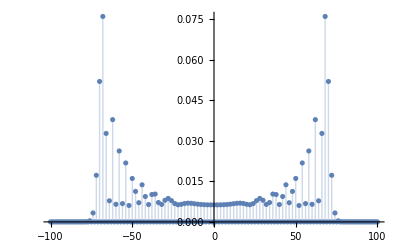

```mathematica
ListPlot[probabilities,PlotRange->All,Filling->Axis]
```

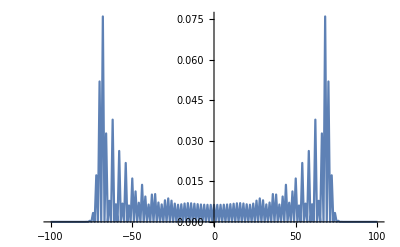

```mathematica
ListPlot[probabilities,PlotRange->All,Joined->True]
```

## Classical Walk

```mathematica
|w[0]⟩=|Subscript[0, ĉ]⟩⊗|Subscript[0, p̂]⟩
```

|0_(ĉ),0_(p̂)⟩

```mathematica
DefineOperatorOnKets[
h,
{|Subscript[0, ĉ]⟩:>(|Subscript[0, ĉ]⟩+|Subscript[1, ĉ]⟩)/(√2),
|Subscript[1, ĉ]⟩:>(|Subscript[0, ĉ]⟩-|Subscript[1, ĉ]⟩)/(√2)}]
```

|0_(ĉ)⟩:>(|0_(ĉ)⟩+|1_(ĉ)⟩)/(√2)
|1_(ĉ)⟩:>(|0_(ĉ)⟩-|1_(ĉ)⟩)/(√2)

```mathematica
DefineOperatorOnKets[
s,
{|Subscript[0, ĉ],Subscript[j_, p̂]⟩:>|Subscript[0, ĉ],Subscript[(j-1), p̂]⟩,
|Subscript[1, ĉ],Subscript[j_, p̂]⟩:>|Subscript[1, ĉ],Subscript[(j+1), p̂]⟩
}
]
```

|0_(ĉ),j__(p̂)⟩:>|0_(ĉ),(j-1)_(p̂)⟩
|1_(ĉ),j__(p̂)⟩:>|1_(ĉ),(j+1)_(p̂)⟩

```mathematica
j=RandomInteger[{-100,100}]
```

53

```mathematica
j
```

53

```mathematica
|Subscript[j, p̂]⟩·⟨Subscript[j, p̂]|
```

|53_(p̂)⟩·⟨53_(p̂)|

```mathematica
list={0}
```

{0}

```mathematica
For[i=-3,i≤ 3,i+=2, 
Print[i];
AppendTo[list, i]];
```

-3

-1

1

3

```mathematica
Append[list, 1]
```

{0,1}

```mathematica
list
```

{0,-3,-1,1,3}

```mathematica
steps=100;
Do[
list={};
For[i=-k,i≤ k,i=i+2, AppendTo[list, i]];
j=RandomInteger[list];
|w[k]⟩=Expand[|Subscript[j, p̂]⟩·⟨Subscript[j, p̂]|·s·h·|w[k-1]⟩],

{k,1,steps,1}];
```

RandomInteger::parb: {-2,0,2} should have between 0 and 2 parameters.

RandomInteger::parb: {-3,-1,1,3} should have between 0 and 2 parameters.

RandomInteger::parb: {-4,-2,0,2,4} should have between 0 and 2 parameters.

General::stop: Further output of RandomInteger::parb will be suppressed during this calculation.

$Aborted

```mathematica
Do[
With[{j=pos},
DefineOperatorOnKets[
pp[j],
{(|Subscript[n_, ĉ],Subscript[k_, p̂]⟩/;k=!=j):>0,
|Subscript[n_, ĉ],Subscript[j, p̂]⟩:>|Subscript[n, ĉ],Subscript[j, p̂]⟩
} ]],
{pos,-steps,steps}]
```

```mathematica
probabilities=
Table[{j,⟨w[steps]|·pp[j]·|w[steps]⟩},{j,-steps,steps}]
```

{{-100,1/1267650600228229401496703205376},{-99,0},{-98,4901/633825300114114700748351602688},{-97,0},{-96,10839217/633825300114114700748351602688},{-95,0},{-94,9563034497/633825300114114700748351602688},{-93,0},{-92,8466857748385/1267650600228229401496703205376},{-91,0},{-90,16600079374029/9903520314283042199192993792},{-89,0},{-88,2541926553484961/9903520314283042199192993792},{-87,0},{-86,248926840792334897/9903520314283042199192993792},{-85,0},{-84,128541760059648576701/79228162514264337593543950336},{-83,0},{-82,2784869761222650907765/39614081257132168796771975168},{-81,0},{-80,81706266359382189552057/39614081257132168796771975168},{-79,0},{-78,1622670239924915814721729/39614081257132168796771975168},{-77,0},{-76,43190880424586143262793781/79228162514264337593543950336},{-75,0},{-74,47072846250456545769509957/9903520314283042199192993792},{-73,0},{-72,257864889397719493119639825/9903520314283042199192993792},{-71,0},{-70,821175424940048731868375033/9903520314283042199192993792},{-69,0},{-68,41311445066036993684904928177/316912650057057350374175801344},{-67,0},{-66,9896611417586560094175048277/158456325028528675187087900672},{-65,0},{-64,1068472086995620246705869937/158456325028528675187087900672},{-63,0},{-62,10267193514234873145822469585/158456325028528675187087900672},{-61,0},{-60,3142422731012132754481099745/316912650057057350374175801344},{-59,0},{-58,413443189053764562114037589/9903520314283042199192993792},{-57,0},{-56,99750463553731878531321113/9903520314283042199192993792},{-55,0},{-54,356363440472471760163683513/9903520314283042199192993792},{-53,0},{-52,411817579827344653908567685/79228162514264337593543950336},{-51,0},{-50,1164530903165889619937138765/39614081257132168796771975168},{-49,0},{-48,513314259221809364148700801/39614081257132168796771975168},{-47,0},{-46,410012267320345497664091417/39614081257132168796771975168},{-45,0},{-44,1878472424660696388649568269/79228162514264337593543950336},{-43,0},{-42,100160820675199091094181645/9903520314283042199192993792},{-41,0},{-40,75269878740182151426234569/9903520314283042199192993792},{-39,0},{-38,174705315510993540201712961/9903520314283042199192993792},{-37,0},{-36,18481036351680951336936196641/1267650600228229401496703205376},{-35,0},{-34,4092499002075254166437111333/633825300114114700748351602688},{-33,0},{-32,4774645652156681994606579665/633825300114114700748351602688},{-31,0},{-30,8094777658233551105695043137/633825300114114700748351602688},{-29,0},{-28,16840581600855613350458169953/1267650600228229401496703205376},{-27,0},{-26,23486558729113438703987733/2475880078570760549798248448},{-25,0},{-24,15677986510370930181819433/2475880078570760549798248448},{-23,0},{-22,15098888079647038706641625/2475880078570760549798248448},{-21,0},{-20,151408223308140466586722141/19807040628566084398385987584},{-19,0},{-18,89890928789341918962203541/9903520314283042199192993792},{-17,0},{-16,94075442405300473695396857/9903520314283042199192993792},{-15,0},{-14,89537651856781877802570017/9903520314283042199192993792},{-13,0},{-12,162655306189311134694086645/19807040628566084398385987584},{-11,0},{-10,18383087540168548611518605/2475880078570760549798248448},{-9,0},{-8,16986658235157812789811161/2475880078570760549798248448},{-7,0},{-6,16168630186613638507701537/2475880078570760549798248448},{-5,0},{-4,504792852233967790920927009/79228162514264337593543950336},{-3,0},{-2,250097860364199466796759205/39614081257132168796771975168},{-1,0},{0,249681897186878552922668961/39614081257132168796771975168},{1,0},{2,249681897186878552922668961/39614081257132168796771975168},{3,0},{4,497753475386998479205553649/79228162514264337593543950336},{5,0},{6,15366639685259145233218437/2475880078570760549798248448},{7,0},{8,14932297288560420972171305/2475880078570760549798248448},{9,0},{10,14150223044052148729346921/2475880078570760549798248448},{11,0},{12,104089777293424763167781117/19807040628566084398385987584},{13,0},{14,46950236425438885966206917/9903520314283042199192993792},{15,0},{16,43580872574679106787389817/9903520314283042199192993792},{17,0},{18,45131578158363897419087985/9903520314283042199192993792},{19,0},{20,106965910611921068205900901/19807040628566084398385987584},{21,0},{22,16380141229043383582806269/2475880078570760549798248448},{23,0},{24,17893528336870241948788633/2475880078570760549798248448},{25,0},{26,15458255765347208386944433/2475880078570760549798248448},{27,0},{28,5206806509920176589286558625/1267650600228229401496703205376},{29,0},{30,2055820989701984754644584837/633825300114114700748351602688},{31,0},{32,3436189380016070233368902609/633825300114114700748351602688},{33,0},{34,5003124275521667233060544993/633825300114114700748351602688},{35,0},{36,7645426718769789137906560641/1267650600228229401496703205376},{37,0},{38,26000109881158152210230885/9903520314283042199192993792},{39,0},{40,52176539176930871203510745/9903520314283042199192993792},{41,0},{42,86072073928376872935615529/9903520314283042199192993792},{43,0},{44,299835645149154671949773669/79228162514264337593543950336},{45,0},{46,153231413407807948434562397/39614081257132168796771975168},{47,0},{48,381287409153546636250715905/39614081257132168796771975168},{49,0},{50,110028951268507669228660361/39614081257132168796771975168},{51,0},{52,551804290552229661122088157/79228162514264337593543950336},{53,0},{54,76116851576363481007675293/9903520314283042199192993792},{55,0},{56,34504371452339715194832713/9903520314283042199192993792},{57,0},{58,107004922585931515913380145/9903520314283042199192993792},{59,0},{60,989413797763676979973769393/316912650057057350374175801344},{61,0},{62,1736106846084511129578799381/158456325028528675187087900672},{63,0},{64,1405729423747679276443137137/158456325028528675187087900672},{65,0},{66,487215780709642636571966737/158456325028528675187087900672},{67,0},{68,6921995092042056310469043745/316912650057057350374175801344},{69,0},{70,209082563882237163814803773/9903520314283042199192993792},{71,0},{72,84137065406475899377608801/9903520314283042199192993792},{73,0},{74,18350614205291332408200257/9903520314283042199192993792},{75,0},{76,19363782743393311354722781/79228162514264337593543950336},{77,0},{78,816702460758409965933925/39614081257132168796771975168},{79,0},{80,45399267070615400761657/39614081257132168796771975168},{81,0},{82,1687270420314486413649/39614081257132168796771975168},{83,0},{84,84112687205079678821/79228162514264337593543950336},{85,0},{86,174588344051257397/9903520314283042199192993792},{87,0},{88,1898985035655185/9903520314283042199192993792},{89,0},{90,13140689486985/9903520314283042199192993792},{91,0},{92,7070578736257/1267650600228229401496703205376},{93,0},{94,8392579397/633825300114114700748351602688},{95,0},{96,9963697/633825300114114700748351602688},{97,0},{98,4705/633825300114114700748351602688},{99,0},{100,1/1267650600228229401496703205376}}

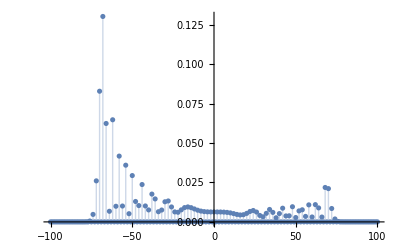

```mathematica
ListPlot[probabilities,PlotRange->All,Filling->Axis]
```

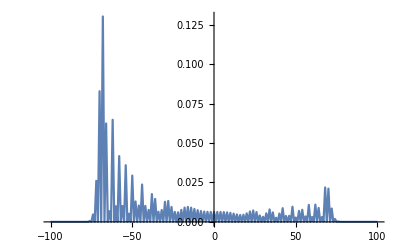

```mathematica
ListPlot[probabilities,PlotRange->All,Joined->True]
```